# LGSBloch

## Generate and solve the Bloch equations describing a laser guide star

```mathematica
PacletManager`PacletDirectoryAdd["~/Development/AtomicDensityMatrix/AtomicDensityMatrix"];
PrependTo[$Path,"~/Development/AtomicDensityMatrix/AtomicDensityMatrix"];
Get["AtomicDensityMatrix/Kernel/init.m"];
```

```mathematica
Get["PhysicalConstants`"]
Get["Units`"]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Global`inModule=True
```

True

```mathematica
Global`inModule=False
```

False

```mathematica
If[Global`inModule,
	Quiet[
	    BeginPackage["LGSBloch`", {"PhysicalConstants`", "Units`", "AtomicDensityMatrix`"}],
	    General::obspkg
	];
];
```

```mathematica
Get["AtomicDensityMatrix`ProcessOptions`"];
Get["AtomicDensityMatrix`"];
```

```mathematica
ExportLGSSystem::usage = "";
IntensitySI::usage = "";
BFieldG::usage = "";
BeamTransitRatePerS::usage = "";
RecoilShiftHz::usage = "";
VccRatePerS::usage = "";
SDampingCollisionRatePerS::usage = "";
MagneticZenithDegrees::usage = "";
MagneticAzimuthDegrees::usage = "";
PolarizationAngleDegrees::usage = "";
EllipticityDegrees::usage = "";
DetuningHz::usage = "";
LaserWidthHz::usage = "";
TemperatureK::usage = "";
RecoilParameter::usage = "";
VccFunction::usage = "";
VelocityGroups::usage = "";
PlotVelocityGroups::usage = "";
QuantumNumbers::usage = "";
StateLabelFunction::usage = "";
```

```mathematica
If[Global`inModule,
	Begin["`Private`"];
];
```

```mathematica
DownValueNames[sym_] := DownValues[sym][[2 ;; , 1, 1, 1]]
```

```mathematica
LGSDefaults["ParanalNoRepump"] = {IntensitySI[Subscript["3S", 1/2]->Subscript["3P", 3/2]] -> 46.,
    EllipticityDegrees[Subscript["3S", 1/2]->Subscript["3P", 3/2]] -> 45.,
    PolarizationAngleDegrees[Subscript["3S", 1/2]->Subscript["3P", 3/2]] -> 0,
    DetuningHz[Subscript["3S", 1/2]->Subscript["3P", 3/2]] -> -6.268*^8,
    LaserWidthHz[Subscript["3S", 1/2]->Subscript["3P", 3/2]] -> 0.,
    BFieldG -> 0.22750,
    MagneticZenithDegrees -> 90.,
    MagneticAzimuthDegrees -> 90.,
    BeamTransitRatePerS -> 131.944,
    VccRatePerS -> 1/(35.0 * 10^-6),
    SDampingCollisionRatePerS -> 4081.63,
    TemperatureK -> 185.,
    RecoilParameter -> 1};

LGSDefaults["ParanalRepump"] = {
    IntensitySI[Subscript["3S", 1/2]&&F==2->Subscript["3P", 3/2]] -> 40.48,
    EllipticityDegrees[Subscript["3S", 1/2]&&F==2->Subscript["3P", 3/2]] -> 45.,
    PolarizationAngleDegrees[Subscript["3S", 1/2]&&F==2->Subscript["3P", 3/2]] -> 0,
    DetuningHz[Subscript["3S", 1/2]&&F==2->Subscript["3P", 3/2]] -> -6.268*^8,
    LaserWidthHz[Subscript["3S", 1/2]&&F==2->Subscript["3P", 3/2]] -> 0.,
    IntensitySI[Subscript["3S", 1/2]&&F==1->Subscript["3P", 3/2]] -> 5.52,
    EllipticityDegrees[Subscript["3S", 1/2]&&F==1->Subscript["3P", 3/2]] -> 45.,
    PolarizationAngleDegrees[Subscript["3S", 1/2]&&F==1->Subscript["3P", 3/2]] -> 0,
    DetuningHz[Subscript["3S", 1/2]&&F==1->Subscript["3P", 3/2]] -> 1.0832*^9,
    LaserWidthHz[Subscript["3S", 1/2]&&F==1->Subscript["3P", 3/2]] -> 0.,
    BFieldG -> 0.22750,
    MagneticZenithDegrees -> 90.,
    MagneticAzimuthDegrees -> 90.,
    BeamTransitRatePerS -> 131.944,
    VccRatePerS -> 1/(35.0 * 10^-6),
    SDampingCollisionRatePerS -> 4081.63,
    TemperatureK -> 185.,
    RecoilParameter -> 1};

LGSDefaults[] := DownValueNames[LGSDefaults];
```

```mathematica
hasZeemanStructure[sys_] := MemberQ[{"Zeeman", "HyperfineZeeman"}, AtomicSystemType@sys]
```

```mathematica
hasHyperfineStructure[sys_] := MemberQ[{"Hyperfine", "HyperfineZeeman"}, AtomicSystemType@sys]
```

```mathematica
valenceN[state_] := PrincipalQuantumNumber@Last@ValenceConfiguration@state
```

```mathematica
nLJ[state_] := Subscript[ToString@valenceN@state <> LSymbol@state, J@state]
```

Change in velocity due to absorbing one photon, in units of the most probable atomic speed

```mathematica
RecoilVelocity[groundState_, excitedState_, temperature_] := Convert[(PlanckConstant(Wavenumber[excitedState] - Wavenumber[groundState]))/(AtomicWeight[groundState] AtomicMassUnit MostProbableSpeed[groundState, temperature]), 1];
```

```mathematica
StateLabels::usage = "";
Options[AtomicSystem] = {StateLabels -> Automatic, DropInexactValues -> False};
OptionProcessor[StateLabels] = Switch[#,
	Automatic,
	Function[states, Range@Length@states],
	OptionsPattern[],
	Function[states, states /. #],
	_List,
	Function[states, PadRight[{}, Length@states, #]],
	_,
	Function[states, # /@ states]
	]&;
InexactExpressionPattern[] = expr_ /; !FreeQ[expr, n_ /; InexactNumberQ[n]];
(AtomicSystem[states_, parameters_, opts : OptionsPattern[]] := Module[{stateLabels, dropInexactValues, fullParameters, system}, 
	fullParameters = Flatten[parameters /. BranchingRatio -> BranchingRatio /@ states];
	system = AtomicState[#, AtomicData[#, fullParameters]]& /@ states /. Thread[states -> stateLabels@states];
	If[dropInexactValues, system = DeleteCases[system, _ -> InexactExpressionPattern[], ∞]];
	system
]) // ProcessOptions;
```

```mathematica
levelPopulations[atomicSystem_] := (First@StateLabel[#] -> Tr@DensityMatrix[#])& /@ GatherBy[atomicSystem, StateLabel]
```

```mathematica
hfStateLabel = Row[{StateLabel@#, "(", F == F@#, ")"}]&;
```

```mathematica
hfStatePopulations[atomicSystem_] := (hfStateLabel@First@# -> Tr@DensityMatrix[#])& /@ Join@@GatherBy[atomicSystem, {StateLabel, F}];
```

```mathematica
SelectDirectedTransitions[sys_, crit_] := Flatten@Pick[DirectSelfProduct[Rule, sys], DirectedTransitionQ[sys, crit]]
```

```mathematica
transitionFrequency[state1_, state2_] := -Subtract@@Diagonal@WignerEckart[{state1, state2}, {Energy, 0, 0}] / (2π)
```

```mathematica
resonanceDetunings[atomicSystem_, pumpTransitions_] := Module[{hfStateLabel, stretchedState, stretchedAtomicSystem, pumpSubsystems, transitionFrequencies, fLabels},
	hfStateLabel = Row[{StateLabel@#, "(", F == F@#, ")"}]&;
    stretchedState = If[AtomicSystemType@atomicSystem == "Toy", True, M == F];
    stretchedAtomicSystem = SelectStates[atomicSystem, stretchedState];
    pumpSubsystems = SelectDirectedTransitions[stretchedAtomicSystem, # && Abs[F - F'] <= 1]& /@ pumpTransitions;
    transitionFrequencies = Apply[transitionFrequency, pumpSubsystems, {2}];
    fLabels = Map[hfStateLabel, pumpSubsystems, {3}];
    Thread[pumpTransitions -> MapThread[Rule, {fLabels, transitionFrequencies}, 2]] /. _Energy -> 0
]
```

```mathematica
shiftedTransitionFrequencies[atomicSystem_, pumpTransitionsNoHF_]  := -2 Pi (Flatten /@ (pumpTransitionsNoHF[[All, All, 1]] /. resonanceDetunings[atomicSystem, pumpTransitionsNoHF[[All, All, 1]]])[[All, All, 2]] - (DetuningHz /@ pumpTransitionsNoHF[[All, All, 1]]))/dopplerWidths[pumpTransitionsNoHF][[All, 2]] // Flatten;
```

```mathematica
naturalWidths[pumpTransitionsNoHF_] := Thread[pumpTransitionsNoHF[[All, 2, 2]] -> (NaturalWidth /@ pumpTransitionsNoHF[[All, 2, 3]])] /. SIUnits
```

```mathematica
decayWavelengths[states_, stateLabelFunction_] := Thread[decays[states, stateLabelFunction] -> 1/Subtract@@@Map[Wavenumber, decays[states, stateLabelFunction], {2}] /. atomicData[states, stateLabelFunction] /. SIUnits];
```

```mathematica
unitPrefixes = {Mega -> 10^6, Nano -> 10^-9};
SIUnits = Join[{Second -> 1,  Centimeter -> 10^7}, unitPrefixes];
```

```mathematica
atomicData[states_, stateLabelFunction_] := Flatten[AtomicData[#, StateLabel -> stateLabelFunction[#]]& /@ states] /. unitPrefixes /. PartialWidth[_][_] -> 0;
```

```mathematica
branchingRatios[states_, stateLabelFunction_] := Flatten@DirectSelfProduct[AtomicData[#2, BranchingRatio[#1], StateLabel -> stateLabelFunction]&, states] /. PartialWidth[_][_] -> 0
```

```mathematica
decays[states_, stateLabelFunction_] := Cases[branchingRatios[states, stateLabelFunction], (BranchingRatio[s1_, s2_] -> x_?Positive) :> s1 -> s2]
```

```mathematica
dopplerWidths[pumpTransitionsNoHF_] := DopplerWidth[#1[[2]] -> #2[[2]]] -> DopplerWidth[#1[[3]], #2[[3]], TemperatureK]& @@@ pumpTransitionsNoHF
```

```mathematica
rabiToIntensity[atomicSystem_, pumpTransitionsNoHF_] := (RabiFrequency[#[[All, 1]]] -> ReducedRabiFrequency[atomicSystem, #[[All, 2]], IntensitySI[#[[All, 1]]] Watt / Meter^2, "SI"])& /@ pumpTransitionsNoHF
```

```mathematica
bohrMagneton = BohrMagneton -> Convert[BohrMagneton/PlanckConstantReduced, Mega / Second / Gauss]
```

BohrMagneton→(8.79411 Mega)/(Gauss Second)

```mathematica
dopplerShifts = DopplerShift[tr_, i_] -> DopplerWidth[tr] VGCenter[i];
```

```mathematica
partition[array_SparseArray, {i_, j_}, ignoreDims_ : 0] := Module[{newDims, indices, permutation},
	newDims = Flatten@{Table[{i, j}, ArrayDepth@array - ignoreDims]};
	indices = Range[ignoreDims + Length@newDims];
	permutation = Flatten@{
		indices[[ignoreDims + 1;;;;2]], 
		Take[indices, ignoreDims], 
		If[Length@indices > ignoreDims + 1, indices[[ignoreDims + 2;;;;2]], {}]
	};
	If[$VersionNumber < 11.2, Normal, Identity]@Transpose[ArrayReshape[array, Join[Take[Dimensions@array, ignoreDims], newDims]], permutation]
]
```

```mathematica
partition[list_List, {i_, j_}, ignoreDims_ : 0] := partition[#, {i, j}, ignoreDims]& /@ list
```

```mathematica
plusToList[a_Plus] := List@@a
plusToList[a_] := a
```

```mathematica
timesToList[a_Times] := List@@a
timesToList[a_] := a
```

```mathematica
MatrixCoefficients[a_, vars_] := SparseArray@Prepend[
	SparseArray@Coefficient[a, #]& /@ Flatten@vars, 
	SparseArray@SparseReplaceAll[a, Alternatives@@Flatten[timesToList /@ vars] -> 0]
];
MatrixCoefficients[a_] := Module[{vars, array}, 
	vars = Union[Times@@@DeleteCases[Variables /@ Flatten[plusToList /@ ArrayRules[a][[All, 2]]], {}]];
	array = N@MatrixCoefficients[a, vars];
	If[array[[1]]@"ExplicitLength" > 0,
		vars = Prepend[vars, 1],
		array = Rest@array
	];
	{vars, array}
];
```

```mathematica
experimentalParameters = {BField -> BFieldG Gauss, BeamTransitRate -> BeamTransitRatePerS / Second,
        RecoilShift -> 2 Pi RecoilShiftHz / Second, VccTime -> VccTimeS Second, SDampingCollisionRate -> SDampingCollisionRatePerS / Second,
        MagneticZenith -> MagneticZenithDegrees Degree, MagneticAzimuth -> MagneticAzimuthDegrees Degree, Ellipticity[transition_] :> EllipticityDegrees[transition] Degree,
        PolarizationAngle[transition_] :> PolarizationAngleDegrees[transition] Degree, LaserWidth[t_] :> 2 Pi LaserWidthHz[t] / Second,
        Detuning[t_] :> 2 Pi DetuningHz[t] / Second, AtomicDensity -> 1, VccRate -> VccRatePerS} // N
```

{BField→BFieldG Gauss,BeamTransitRate→BeamTransitRatePerS/Second,RecoilShift→(6.28319 RecoilShiftHz)/Second,VccTime→Second VccTimeS,SDampingCollisionRate→SDampingCollisionRatePerS/Second,MagneticZenith→0.0174533 MagneticZenithDegrees,MagneticAzimuth→0.0174533 MagneticAzimuthDegrees,Ellipticity[transition_]:>EllipticityDegrees[transition] 0.0174533,PolarizationAngle[transition_]:>PolarizationAngleDegrees[transition] 0.0174533,LaserWidth[t_]:>(2. 3.14159 LaserWidthHz[t])/Second,Detuning[t_]:>(2. 3.14159 DetuningHz[t])/Second,AtomicDensity→1.,VccRate→VccRatePerS}

```mathematica
otherVG[i_] := 3 - i;
```

```mathematica
(* Hard collisions assumption: probability to end up in any v.g. is proportional to Maxwell-Boltzmann distribution *)
hardCollisions = VccRate[i_, j_] -> VccRate[i] VGDensity[j];
(* Uniform VCC assumption: VCC rate is independent of velocity group *)
uniformVCC = VccRate[_] -> VccRate;
(* Total VGDensity is one *)
vgDensityNormalization = VGDensity[j_] -> (1 - VGDensity[otherVG[j]]);
```

```mathematica
Options[LGSGenerateSystem] = {
    QuantumNumbers -> {J, L, S, NuclearSpin},
    StateLabelFunction -> nLJ,
    NeglectedElements -> (StateLabel' == StateLabel && F' != F)
};
OptionProcessor[QuantumNumbers] = # /. {Automatic | All -> {J, L, S, NuclearSpin}, None -> {}}&;
OptionValidator[QuantumNumbers] = list_List /; SubsetQ[{J, L, S, NuclearSpin}, list];

LGSGenerateSystem[{atom_String, line_String}, pumpTransitions_, opts : OptionsPattern[]] :=
    LGSGenerateSystem[AtomicTransition[atom, line], pumpTransitions, opts];
```

```mathematica
(*states = AtomicTransition@@{"Na", "D1"}
pumpTransitions = {Subscript["3S", 1/2] -> Subscript["3P", 1/2]}*)
```

```mathematica
(*states = {
	{"Na", 23, {"Ne", {3, "s"}}, {2, "S", 1/2}},
	{"Na", 23, {"Ne", {3, "p"}}, {2, "P", 1/2}},
	{"Na", 23, {"Ne", {3, "p"}}, {2, "P", 3/2}},
	{"Na", 23, {"Ne", {4, "s"}}, {2, "S", 1/2}},
	{"Na", 23, {"Ne", {3, "d"}}, {2, "D", 3/2}},
	{"Na", 23, {"Ne", {3, "d"}}, {2, "D", 5/2}},
	{"Na", 23, {"Ne", {4, "p"}}, {2, "P", 3/2}}
};
pumpTransitions = {Subscript["3S", 1/2] -> Subscript["4P", 3/2]};*)
```

```mathematica
(*quantumNumbers={};
stateLabelFunction=nLJ;
printDiagrams=True;
neglectedElements = (StateLabel' == StateLabel && F' != F);
opts={};*)
```

```mathematica
populationOperator[atomicSystem_, crits_] := DMVariables[atomicSystem] /. ({Alternatives@@Diagonal@DensityMatrix@SelectStates[atomicSystem, #] -> 1}&/@ crits) /. DMElementPattern[] -> 0 // SparseArray
```

```mathematica
generateAtomicSystem[states_, pumpTransitions_, stateLabelFunction_,quantumNumbers_,neglectedElements_]:= Module[{dataSI, stateLabels, interactionStates, systemParameters,toyAtomicSystem,groundStateLabels,excitedStateLabels,atomicSystem,pumpTransitionsNoHF,nonPumpCoherences},
dataSI = atomicData[states, stateLabelFunction] /. SIUnits;
stateLabels = stateLabelFunction /@ states;
interactionStates = Or @@ Union@Flatten[List @@@ pumpTransitions, 1] /. Thread[stateLabels -> Thread[StateLabel == stateLabels]];systemParameters = Flatten@{quantumNumbers, Parity, Energy, NaturalWidth, BranchingRatio};toyAtomicSystem = DeleteCases[AtomicSystem[states, systemParameters, StateLabels -> stateLabelFunction, DropInexactValues -> True], BranchingRatio[_]->1, ∞];groundStateLabels = StateLabel@GroundStates@toyAtomicSystem;excitedStateLabels = StateLabel@ExcitedStates@toyAtomicSystem;atomicSystem = Sublevels[toyAtomicSystem];pumpTransitionsNoHF = Map[Prepend[StateLabel@SelectState[atomicSystem, #] /. Thread[stateLabels -> Transpose@{stateLabels, states}], #]&, pumpTransitions, {2}];nonPumpCoherences = !interactionStates && StateLabel != StateLabel';
    SetOptions[DensityMatrix, TimeDependence -> False, ComplexExpandVariables -> Subscript, NeglectedElements -> nonPumpCoherences || neglectedElements];
{dataSI, stateLabels,toyAtomicSystem,groundStateLabels,excitedStateLabels,atomicSystem,pumpTransitionsNoHF}
]
```

```mathematica
(*states = {
	{"Na", 23, {"Ne", {3, "s"}}, {2, "S", 1/2}},
	{"Na", 23, {"Ne", {3, "p"}}, {2, "P", 1/2}},
	{"Na", 23, {"Ne", {3, "p"}}, {2, "P", 3/2}},
	{"Na", 23, {"Ne", {4, "s"}}, {2, "S", 1/2}},
	{"Na", 23, {"Ne", {3, "d"}}, {2, "D", 3/2}},
	{"Na", 23, {"Ne", {3, "d"}}, {2, "D", 5/2}},
	{"Na", 23, {"Ne", {4, "p"}}, {2, "P", 3/2}}
};
pumpTransitions = {Subscript["3S", 1/2] -> Subscript["4P", 3/2]};
quantumNumbers={J, L, S, NuclearSpin};*)
```

```mathematica
states = AtomicTransition@@{"Na", "D1"};
pumpTransitions = {Subscript["3S", 1/2] -> Subscript["3P", 1/2]};
quantumNumbers={};
```

```mathematica
stateLabelFunction=nLJ;
neglectedElements = (StateLabel' == StateLabel && F' != F);
```

```mathematica
{dataSI, stateLabels, toyAtomicSystem, groundStateLabels, excitedStateLabels, atomicSystem, pumpTransitionsNoHF} = generateAtomicSystem[states, pumpTransitions, stateLabelFunction, quantumNumbers, neglectedElements]
```

{{ElementName[(3S)_(1/2)]→Sodium,ElementSymbol[(3S)_(1/2)]→Na,AtomicNumber[(3S)_(1/2)]→11,AtomicWeight[(3S)_(1/2)]→23,Abundance[(3S)_(1/2)]→1,NuclearSpin[(3S)_(1/2)]→3/2,J[(3S)_(1/2)]→1/2,L[(3S)_(1/2)]→0,S[(3S)_(1/2)]→1/2,NaturalWidth[(3S)_(1/2)]→0,Energy[(3S)_(1/2)]→0,HyperfineA[(3S)_(1/2)]→5.56573×10^9,HyperfineB[(3S)_(1/2)]→0,Parity[(3S)_(1/2)]→Even,Wavenumber[(3S)_(1/2)]→0,Lifetime[(3S)_(1/2)]→∞,ElementName[(3P)_(1/2)]→Sodium,ElementSymbol[(3P)_(1/2)]→Na,AtomicNumber[(3P)_(1/2)]→11,AtomicWeight[(3P)_(1/2)]→23,Abundance[(3P)_(1/2)]→1,NuclearSpin[(3P)_(1/2)]→3/2,J[(3P)_(1/2)]→1/2,L[(3P)_(1/2)]→1,S[(3P)_(1/2)]→1/2,NaturalWidth[(3P)_(1/2)]→6.14×10^7,Energy[(3P)_(1/2)]→3.19395×10^15,HyperfineA[(3P)_(1/2)]→5.93384×10^8,HyperfineB[(3P)_(1/2)]→0,Parity[(3P)_(1/2)]→Odd,Wavenumber[(3P)_(1/2)]→0.00169562,Lifetime[(3P)_(1/2)]→1.6299×10^-8},{(3S)_(1/2),(3P)_(1/2)},{AtomicState[(3S)_(1/2),Parity→Even,Energy→0,NaturalWidth→0,BranchingRatio[(3S)_(1/2)]→0,BranchingRatio[(3P)_(1/2)]→0],AtomicState[(3P)_(1/2),Parity→Odd,BranchingRatio[(3P)_(1/2)]→0]},{(3S)_(1/2)},{(3P)_(1/2)},{AtomicState[(3S)_(1/2),Parity→Even,Energy→0,NaturalWidth→0,BranchingRatio[(3S)_(1/2)]→0,BranchingRatio[(3P)_(1/2)]→0],AtomicState[(3P)_(1/2),Parity→Odd,BranchingRatio[(3P)_(1/2)]→0]},{{(3S)_(1/2),(3S)_(1/2),{Na,23,{Ne,{3,s}},{2,S,1/2}}}→{(3P)_(1/2),(3P)_(1/2),{Na,23,{Ne,{3,p}},{2,P,1/2}}}}}

```mathematica
atomicSystem
```

{AtomicState[(3S)_(1/2),Parity→Even,Energy→0,NaturalWidth→0,BranchingRatio[(3S)_(1/2)]→0,BranchingRatio[(3P)_(1/2)]→0],AtomicState[(3P)_(1/2),Parity→Odd,BranchingRatio[(3P)_(1/2)]→0]}

```mathematica
generateExperimentalSystem[pumpTransitions_, pumpTransitionsNoHF_, atomicSystem_] := Module[{opticalParameters, experimentalSystem},
	(* Define experimental system. The two regions represent two velocity groups. *)
    opticalParameters = MapThread[{
        -Subtract @@ Energy /@ #1 + Detuning[#2] - DopplerShift[#1, v],
        RabiFrequency[#2] / ReducedME[Sort[#1][[1]], {Dipole, 1}, Sort[#1][[2]]],
        If[hasZeemanStructure@atomicSystem, {PolarizationAngle[#2], Ellipticity[#2]}, {}],
        AllowedCouplings -> #2,
        OpticalWidth -> LaserWidth[#2]
    }&, {pumpTransitionsNoHF[[All, All, 2]], pumpTransitions}];
    experimentalSystem = Table[
        ExperimentalRegion[v, {
            TransitRate[VoidRegion] -> BeamTransitRate,
            TransitRate[otherVG[v]] -> VccRate[v, otherVG[v]],
            Density -> AtomicDensity VGDensity[v],
            OpticalParameters -> opticalParameters,
            MagneticField -> {BField {
                Cos[MagneticAzimuth] Sin[MagneticZenith],
                Sin[MagneticAzimuth] Sin[MagneticZenith],
                Cos[MagneticZenith]
            }, AllowedCouplings -> F == F'},
            (*VelocityGroupRecoilMomentum[otherVG[v]] -> If[v == 1, AtomicMass VGWidth[1], Infinity],*)
            VelocityGroupRecoilMomentum[otherVG[v]] -> -VGWidth[otherVG[v]],
            SDampingRate -> SDampingCollisionRate
        }],
        {v, 2}
    ] /. Thread[Energy/@StateLabel@atomicSystem -> Energy@atomicSystem];
    {opticalParameters, experimentalSystem}
]
```

```mathematica
{opticalParameters, experimentalSystem} = generateExperimentalSystem[pumpTransitions, pumpTransitionsNoHF, atomicSystem]
```

{{{Detuning[(3S)_(1/2)→(3P)_(1/2)]-DopplerShift[(3S)_(1/2)→(3P)_(1/2),v]+Energy[(3P)_(1/2)]-Energy[(3S)_(1/2)],RabiFrequency[(3S)_(1/2)→(3P)_(1/2)]/ReducedME[(3P)_(1/2),{Dipole,1},(3S)_(1/2)],{},AllowedCouplings→(3S)_(1/2)→(3P)_(1/2),OpticalWidth→LaserWidth[(3S)_(1/2)→(3P)_(1/2)]}},{ExperimentalRegion[1,TransitRate[VoidRegion]→BeamTransitRate,TransitRate[2]→VccRate[1,2],Density→AtomicDensity VGDensity[1],OpticalParameters→{{Detuning[(3S)_(1/2)→(3P)_(1/2)]-DopplerShift[(3S)_(1/2)→(3P)_(1/2),1]+Energy[(3P)_(1/2)],RabiFrequency[(3S)_(1/2)→(3P)_(1/2)]/ReducedME[(3P)_(1/2),{Dipole,1},(3S)_(1/2)],{},AllowedCouplings→(3S)_(1/2)→(3P)_(1/2),OpticalWidth→LaserWidth[(3S)_(1/2)→(3P)_(1/2)]}},MagneticField→{{BField Cos[MagneticAzimuth] Sin[MagneticZenith],BField Sin[MagneticAzimuth] Sin[MagneticZenith],BField Cos[MagneticZenith]},AllowedCouplings→F==F'},VelocityGroupRecoilMomentum[2]→-VGWidth[2],SDampingRate→SDampingCollisionRate],ExperimentalRegion[2,TransitRate[VoidRegion]→BeamTransitRate,TransitRate[1]→VccRate[2,1],Density→AtomicDensity VGDensity[2],OpticalParameters→{{Detuning[(3S)_(1/2)→(3P)_(1/2)]-DopplerShift[(3S)_(1/2)→(3P)_(1/2),2]+Energy[(3P)_(1/2)],RabiFrequency[(3S)_(1/2)→(3P)_(1/2)]/ReducedME[(3P)_(1/2),{Dipole,1},(3S)_(1/2)],{},AllowedCouplings→(3S)_(1/2)→(3P)_(1/2),OpticalWidth→LaserWidth[(3S)_(1/2)→(3P)_(1/2)]}},MagneticField→{{BField Cos[MagneticAzimuth] Sin[MagneticZenith],BField Sin[MagneticAzimuth] Sin[MagneticZenith],BField Cos[MagneticZenith]},AllowedCouplings→F==F'},VelocityGroupRecoilMomentum[1]→-VGWidth[1],SDampingRate→SDampingCollisionRate]}}

```mathematica
opticalParameters
```

{{Detuning[(3S)_(1/2)→(3P)_(1/2)]-DopplerShift[(3S)_(1/2)→(3P)_(1/2),v]+Energy[(3P)_(1/2)]-Energy[(3S)_(1/2)],RabiFrequency[(3S)_(1/2)→(3P)_(1/2)]/ReducedME[(3P)_(1/2),{Dipole,1},(3S)_(1/2)],{},AllowedCouplings→(3S)_(1/2)→(3P)_(1/2),OpticalWidth→LaserWidth[(3S)_(1/2)→(3P)_(1/2)]}}

```mathematica
levelDiagramToy[toyAtomicSystem_,opticalParameters_, dataSI_]:= Module[{h0},
h0=Hamiltonian[DeleteParameter[toyAtomicSystem,J],ExperimentalRegion[1, OpticalParameters->opticalParameters]]/.dataSI;
h0=h0/Max@Diagonal[h0];
LevelDiagram[toyAtomicSystem, h0,
StateLabel -> True,
            StateLabelPosition -> Automatic,
            LevelSpacing -> {.01, .007},
MinLabelSpacing->.05,
LevelLength->.2,
ParityOffset->True,
            ImageSize->Small
]/."InlineMath"->"InlineFormula"/.Style[x_,opts___]:>Style[x/.Rational[a_,b_]->Row@{a,"/",b},opts]
]
```

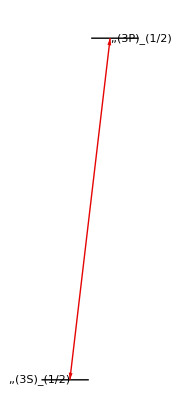

```mathematica
levelDiagramToy[toyAtomicSystem,opticalParameters, dataSI]
```

```mathematica
levelDiagramToScale[atomicSystem_,dataSI_]:= Module[{h0},
h0=Normalize[Hamiltonian[atomicSystem]/.{hb_HyperfineB->10^4 hb, ha_HyperfineA->10^4 ha}/.dataSI, Max];
LevelDiagram[atomicSystem, 
h0,
ArrowStyle->Arrowheads[0,0], 
ParityOffset->True,
ImageSize->Small,
StateLabel->True,
LevelLength->.02,
LevelSpacing->.01,
MinLabelSpacing->.05,
StateLabelPosition->Automatic
]/."InlineMath"->"InlineFormula"/.Style[x_,opts___]:>Style[x/.Rational[a_,b_]->Row@{a,"/",b},opts]
]
```

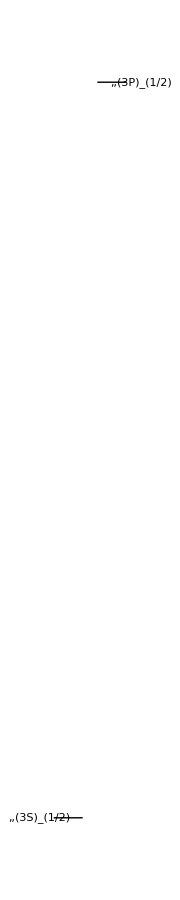

```mathematica
levelDiagramToScale[atomicSystem,dataSI]
```

```mathematica
levelDiagramNotToScale[atomicSystem_,stateLabels_]:= Module[{h0},
h0 = Normalize[Hamiltonian[atomicSystem]/.Thread[Energy/@stateLabels->Range@Length@stateLabels-1]/.{hb_HyperfineB->.02, ha_HyperfineA->.05},Max];
LevelDiagram[atomicSystem, 
h0,
ArrowStyle->Arrowheads[0,0], 
ParityOffset->True,
ImageSize->Small,
StateLabel->True,
LevelLength->.02,
LevelSpacing->.01,
MinLabelSpacing->.05,
StateLabelPosition->Automatic
]/."InlineMath"->"InlineFormula"/.Style[x_,opts___]:>Style[x/.Rational[a_,b_]->Row@{a,"/",b},opts]
]
```

```mathematica
levelDiagramNotToScale[atomicSystem,stateLabels]
```

-Graphics-

```mathematica
generateEquations[atomicSystem_, experimentalSystem_, dataSI_, states_, stateLabels_, stateLabelFunction_, pumpTransitionsNoHF_] := Module[
	{h, hRWA, repopulation, relaxation, recoil, recoilFactors, noVccCoherenceTransfer, eqsN, vars, substituteNumericalParameters, fluorescence},
    (* Define Hamiltonian, repopulation and relaxation matrices. *)
    h = Hamiltonian[atomicSystem, experimentalSystem];
	hRWA = RotatingWaveApproximation[atomicSystem, experimentalSystem, h];
	repopulation = Repopulation[atomicSystem, experimentalSystem] + OpticalBroadening[atomicSystem, experimentalSystem] /. _Wavenumber -> 0 // Expand;
	relaxation = Relaxation[atomicSystem, experimentalSystem];
	(*Make uniform hard collisions assumption for VCC*)
	{repopulation, relaxation} = {repopulation, relaxation} /. hardCollisions /. uniformVCC;
	recoil = OpticalRepopulation[atomicSystem, experimentalSystem][[1]] /. 
		Append[BranchingRatio@@# -> RecoilVelocity[#] BranchingRatio@@# VGInverseWidth[1]& /@ Reverse /@ pumpTransitionsNoHF[[All, All, 2]], _BranchingRatio -> 0];
	repopulation = repopulation + {-recoil, recoil};
	(*For VCC relaxation, v.g. #1  relaxes at a rate VccRate * VGDensity[2] = VccRate * (1 - VGDensity[1]) *)
	relaxation = relaxation /. {VccRate VGDensity[other_] :> VccRate(1 - VGDensity[3 - other])};
	recoilFactors = RecoilVelocity[stateLabelFunction@#1 -> stateLabelFunction@#2] -> RecoilParameter RecoilVelocity[#2, #1, TemperatureK]& @@@ (decays[states, stateLabelFunction] /. Thread[stateLabels -> states]);
	noVccCoherenceTransfer = {x : VGDensity[_] VccRate DMElementPattern[] /;  StateLabel1 == StateLabel2 && F1 == F2 :> x, VGDensity[_] VccRate DMElementPattern[] -> 0};
    eqsN = LiouvilleEquation[atomicSystem, experimentalSystem, hRWA, relaxation, repopulation] /. noVccCoherenceTransfer /. branchingRatios[states, stateLabelFunction] /. dataSI /. SIUnits;
	vars = DMVariables[atomicSystem, experimentalSystem];
	substituteNumericalParameters = # /. dopplerShifts /. dopplerWidths[pumpTransitionsNoHF] /. 
		rabiToIntensity[atomicSystem, pumpTransitionsNoHF] /. bohrMagneton  /. dataSI /. experimentalParameters /. SIUnits /. recoilFactors /. branchingRatios[states, stateLabelFunction]&;
	fluorescence = Sum[Fluorescence[atomicSystem, #, 0, 0, DMLabel -> i], {i, 2}] / (Subtract @@ Energy /@ #)& /@ decays[states, stateLabelFunction] /. branchingRatios[states, stateLabelFunction] /. dataSI /. SIUnits // Expand;
	{eqsN, vars, substituteNumericalParameters, fluorescence}
]
```

```mathematica
{eqsN, vars, substituteNumericalParameters, fluorescence} = generateEquations[atomicSystem, experimentalSystem, dataSI, states, stateLabels, stateLabelFunction, pumpTransitionsNoHF]
```

{{0==RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))+6.14×10^7 ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,1,(3S)_(1/2),(3S)_(1/2))-VccRate ρ_(Re,1,(3S)_(1/2),(3S)_(1/2))+AtomicDensity BeamTransitRate VGDensity[1]+VccRate ρ_(Re,1,(3S)_(1/2),(3S)_(1/2)) VGDensity[1]+VccRate ρ_(Re,2,(3S)_(1/2),(3S)_(1/2)) VGDensity[1]-6.14×10^7 RecoilVelocity[(3P)_(1/2)→(3S)_(1/2)] ρ_(Re,1,(3P)_(1/2),(3P)_(1/2)) VGInverseWidth[1],0==Detuning[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-DopplerShift[(3S)_(1/2)→(3P)_(1/2),1] ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-3.07×10^7 ρ_(Re,1,(3S)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,1,(3S)_(1/2),(3P)_(1/2))-VccRate ρ_(Re,1,(3S)_(1/2),(3P)_(1/2))-1/2 LaserWidth[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,1,(3S)_(1/2),(3P)_(1/2)),0==-3.07×10^7 ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-VccRate ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-1/2 LaserWidth[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))+1/2 RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))-Detuning[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,1,(3S)_(1/2),(3P)_(1/2))+DopplerShift[(3S)_(1/2)→(3P)_(1/2),1] ρ_(Re,1,(3S)_(1/2),(3P)_(1/2))-1/2 RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,1,(3S)_(1/2),(3S)_(1/2)),0==-RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,1,(3S)_(1/2),(3P)_(1/2))-6.14×10^7 ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))-VccRate ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))+VccRate ρ_(Re,1,(3P)_(1/2),(3P)_(1/2)) VGDensity[1]+VccRate ρ_(Re,2,(3P)_(1/2),(3P)_(1/2)) VGDensity[1],0==RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))+6.14×10^7 ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,2,(3S)_(1/2),(3S)_(1/2))-VccRate ρ_(Re,2,(3S)_(1/2),(3S)_(1/2))+AtomicDensity BeamTransitRate VGDensity[2]+VccRate ρ_(Re,1,(3S)_(1/2),(3S)_(1/2)) VGDensity[2]+VccRate ρ_(Re,2,(3S)_(1/2),(3S)_(1/2)) VGDensity[2]+6.14×10^7 RecoilVelocity[(3P)_(1/2)→(3S)_(1/2)] ρ_(Re,1,(3P)_(1/2),(3P)_(1/2)) VGInverseWidth[1],0==Detuning[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-DopplerShift[(3S)_(1/2)→(3P)_(1/2),2] ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-3.07×10^7 ρ_(Re,2,(3S)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,2,(3S)_(1/2),(3P)_(1/2))-VccRate ρ_(Re,2,(3S)_(1/2),(3P)_(1/2))-1/2 LaserWidth[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,2,(3S)_(1/2),(3P)_(1/2)),0==-3.07×10^7 ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-VccRate ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-1/2 LaserWidth[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))+1/2 RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))-Detuning[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,2,(3S)_(1/2),(3P)_(1/2))+DopplerShift[(3S)_(1/2)→(3P)_(1/2),2] ρ_(Re,2,(3S)_(1/2),(3P)_(1/2))-1/2 RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Re,2,(3S)_(1/2),(3S)_(1/2)),0==-RabiFrequency[(3S)_(1/2)→(3P)_(1/2)] ρ_(Im,2,(3S)_(1/2),(3P)_(1/2))-6.14×10^7 ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))-BeamTransitRate ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))-VccRate ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))+VccRate ρ_(Re,1,(3P)_(1/2),(3P)_(1/2)) VGDensity[2]+VccRate ρ_(Re,2,(3P)_(1/2),(3P)_(1/2)) VGDensity[2]},{ρ_(Re,1,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,1,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,1,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,1,(3P)_(1/2),(3P)_(1/2)),ρ_(Re,2,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,2,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,2,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))},#1/.dopplerShifts/.dopplerWidths[{{(3S)_(1/2),(3S)_(1/2),{Na,23,{Ne,{3,s}},{2,S,1/2}}}→{(3P)_(1/2),(3P)_(1/2),{Na,23,{Ne,{3,p}},{2,P,1/2}}}}]/.rabiToIntensity[{AtomicState[(3S)_(1/2),Parity→Even,Energy→0,NaturalWidth→0,BranchingRatio[(3S)_(1/2)]→0,BranchingRatio[(3P)_(1/2)]→0],AtomicState[(3P)_(1/2),Parity→Odd,BranchingRatio[(3P)_(1/2)]→0]},{{(3S)_(1/2),(3S)_(1/2),{Na,23,{Ne,{3,s}},{2,S,1/2}}}→{(3P)_(1/2),(3P)_(1/2),{Na,23,{Ne,{3,p}},{2,P,1/2}}}}]/.bohrMagneton/.{ElementName[(3S)_(1/2)]→Sodium,ElementSymbol[(3S)_(1/2)]→Na,AtomicNumber[(3S)_(1/2)]→11,AtomicWeight[(3S)_(1/2)]→23,Abundance[(3S)_(1/2)]→1,NuclearSpin[(3S)_(1/2)]→3/2,J[(3S)_(1/2)]→1/2,L[(3S)_(1/2)]→0,S[(3S)_(1/2)]→1/2,NaturalWidth[(3S)_(1/2)]→0,Energy[(3S)_(1/2)]→0,HyperfineA[(3S)_(1/2)]→5.56573×10^9,HyperfineB[(3S)_(1/2)]→0,Parity[(3S)_(1/2)]→Even,Wavenumber[(3S)_(1/2)]→0,Lifetime[(3S)_(1/2)]→∞,ElementName[(3P)_(1/2)]→Sodium,ElementSymbol[(3P)_(1/2)]→Na,AtomicNumber[(3P)_(1/2)]→11,AtomicWeight[(3P)_(1/2)]→23,Abundance[(3P)_(1/2)]→1,NuclearSpin[(3P)_(1/2)]→3/2,J[(3P)_(1/2)]→1/2,L[(3P)_(1/2)]→1,S[(3P)_(1/2)]→1/2,NaturalWidth[(3P)_(1/2)]→6.14×10^7,Energy[(3P)_(1/2)]→3.19395×10^15,HyperfineA[(3P)_(1/2)]→5.93384×10^8,HyperfineB[(3P)_(1/2)]→0,Parity[(3P)_(1/2)]→Odd,Wavenumber[(3P)_(1/2)]→0.00169562,Lifetime[(3P)_(1/2)]→1.6299×10^-8}/.experimentalParameters/.SIUnits/.recoilFactors$30267/.branchingRatios[{{Na,23,{Ne,{3,s}},{2,S,1/2}},{Na,23,{Ne,{3,p}},{2,P,1/2}}},nLJ]&,{4.88606×10^6 ρ_(Re,1,(3P)_(1/2),(3P)_(1/2))+4.88606×10^6 ρ_(Re,2,(3P)_(1/2),(3P)_(1/2))}}

```mathematica
restrict[{coefficients_, matrix_}, var_] := Module[{},
	mask = !FreeQ[#, var]& /@ coefficients;
	{Pick[coefficients, mask], SparseArray@Pick[matrix, mask]}
]
```

```mathematica
remove[{coefficients_, matrix_}, var_] := Module[{},
	mask = FreeQ[#, var]& /@ coefficients;
	{Pick[coefficients, mask], SparseArray@Pick[matrix, mask]}
]
```

```mathematica
generateMatrices[atomicSystem_, experimentalSystem_, stateLabels_, groundStateLabels_, excitedStateLabels_, substituteNumericalParameters_, vars_, eqsN_, fluorescence_] := Module[{
		nRegions, nVars, B1, B2, A11, A12, A21, A22, Fl1, A11NoVCC, A12VCC, A21Recoil, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator,
		inputParameters, A11NoVCCVGCenter, A11NoVCCVGWidth, A11NoVCCVGInd
	},
    nRegions = Length[experimentalSystem];
    nVars = Length[vars] / Length[experimentalSystem];
    {{B1, B2}, {{A11, A12}, {A21, A22}}} = partition[CoefficientArrays[eqsN[[All, 2]], vars], {nRegions, nVars}];
	Fl1 = partition[CoefficientArrays[fluorescence, vars], {nRegions, nVars}, 1][[2, 1]];
	{A11NoVCC, A12VCC, A21Recoil, B1, Fl1, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator} = MatrixCoefficients /@  {
        SparseReplaceAll[A11, {VccRate VGDensity[_] -> 0}], 
        A12,
        SparseReplaceAll[A21, {VccRate -> 0}],
        B1, 
        Fl1,
        populationOperator[atomicSystem, {All}],
        populationOperator[atomicSystem, stateLabels],
        populationOperator[atomicSystem, groundStateLabels],
        populationOperator[atomicSystem, excitedStateLabels]
    } // substituteNumericalParameters;
    inputParameters = Variables[{A11NoVCC, A12VCC, A21Recoil, B1, Fl1}[[All, 1]] /. {Cos|Sin -> Identity}];
    A11NoVCC = A11NoVCC /. VGWidth[1] -> 1/VGInverseWidth[1];
    A11NoVCCVGCenter = restrict[A11NoVCC, VGCenter[1]];
	A11NoVCCVGWidth = restrict[A11NoVCC, VGInverseWidth[1]];
	A11NoVCCVGInd = remove[A11NoVCC, VGCenter[1]|VGInverseWidth[1]];
    {
        nVars, DMVariables[atomicSystem], B1, Fl1, A11NoVCC, A12VCC, A21Recoil, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator, inputParameters, 
        A11NoVCCVGCenter, A11NoVCCVGWidth, A11NoVCCVGInd
    }
]
```

```mathematica
{nVars, vars, B1, Fl1, A11NoVCC, A12VCC, A21Recoil, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator, inputParameters, A11NoVCCVGCenter, A11NoVCCVGWidth, A11NoVCCVGInd} = 
		generateMatrices[atomicSystem, experimentalSystem, stateLabels, groundStateLabels, excitedStateLabels, substituteNumericalParameters, vars, eqsN, fluorescence]
```

{4,{ρ_(Re,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,(3P)_(1/2),(3P)_(1/2))},{{1. BeamTransitRatePerS VGDensity[1]},SparseArray[…]},{{1},SparseArray[…]},{{1,BeamTransitRatePerS,VccRatePerS,6.28319 DetuningHz[(3S)_(1/2)→(3P)_(1/2)],2.86468×10^8 √TemperatureK VGCenter[1],6.28319 LaserWidthHz[(3S)_(1/2)→(3P)_(1/2)],5.50205×10^6 √IntensitySI[(3S)_(1/2)→(3P)_(1/2)],(0.00109405 RecoilParameter VGInverseWidth[1])/(√TemperatureK)},SparseArray[…]},{{VccRatePerS VGDensity[1]},SparseArray[…]},{{(0.00109405 RecoilParameter VGInverseWidth[1])/(√TemperatureK)},SparseArray[…]},{{1},SparseArray[…]},{{1},SparseArray[…]},{{1},SparseArray[…]},{{1},SparseArray[…]},{BeamTransitRatePerS,RecoilParameter,TemperatureK,VccRatePerS,DetuningHz[(3S)_(1/2)→(3P)_(1/2)],IntensitySI[(3S)_(1/2)→(3P)_(1/2)],LaserWidthHz[(3S)_(1/2)→(3P)_(1/2)],VGCenter[1],VGDensity[1],VGInverseWidth[1]},{{2.86468×10^8 √TemperatureK VGCenter[1]},SparseArray[…]},{{(0.00109405 RecoilParameter VGInverseWidth[1])/(√TemperatureK)},SparseArray[…]},{{1,BeamTransitRatePerS,VccRatePerS,6.28319 DetuningHz[(3S)_(1/2)→(3P)_(1/2)],6.28319 LaserWidthHz[(3S)_(1/2)→(3P)_(1/2)],5.50205×10^6 √IntensitySI[(3S)_(1/2)→(3P)_(1/2)]},SparseArray[…]}}

```mathematica
inputParameters
```

{BeamTransitRatePerS,RecoilParameter,TemperatureK,VccRatePerS,DetuningHz[(3S)_(1/2)→(3P)_(1/2)],IntensitySI[(3S)_(1/2)→(3P)_(1/2)],LaserWidthHz[(3S)_(1/2)→(3P)_(1/2)],VGCenter[1],VGDensity[1],VGInverseWidth[1]}

```mathematica
(LGSGenerateSystem[states_, pumpTransitions_, opts : OptionsPattern[]] := Module[{
		quantumNumbers, stateLabelFunction, neglectedElements, 
		dataSI, stateLabels, toyAtomicSystem, groundStateLabels, excitedStateLabels, atomicSystem, pumpTransitionsNoHF, 
		opticalParameters, experimentalSystem,
		eqsN, vars, substituteNumericalParameters, fluorescence,
		nVars,  B1, Fl1, A11NoVCC, A12VCC, A21Recoil, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator, inputParameters, 
	    A11NoVCCVGCenter, A11NoVCCVGWidth, A11NoVCCVGInd,
	    dmSource, dmRange
	},
	{dataSI, stateLabels, toyAtomicSystem, groundStateLabels, excitedStateLabels, atomicSystem, pumpTransitionsNoHF} = generateAtomicSystem[states, pumpTransitions, stateLabelFunction, quantumNumbers, neglectedElements];    
	{opticalParameters, experimentalSystem} = generateExperimentalSystem[pumpTransitions, pumpTransitionsNoHF, atomicSystem];
	{eqsN, vars, substituteNumericalParameters, fluorescence} = generateEquations[atomicSystem, experimentalSystem, dataSI, states, stateLabels, stateLabelFunction, pumpTransitionsNoHF];
	{nVars, vars, B1, Fl1, A11NoVCC, A12VCC, A21Recoil, totalPopulationOperator, levelPopulationOperator, groundLevelPopulationOperator, excitedLevelPopulationOperator, inputParameters, A11NoVCCVGCenter, A11NoVCCVGWidth, A11NoVCCVGInd} = 
	generateMatrices[atomicSystem, experimentalSystem, stateLabels, groundStateLabels, excitedStateLabels, substituteNumericalParameters, vars, eqsN, fluorescence];
    dmSource = {"Density matrix (source)", vars};
    dmRange = {"Density matrix (range)", vars};
    LGSSystem[
        decays[states, stateLabelFunction], 
        decayWavelengths[states, stateLabelFunction], 
        nVars,
        Append[A11NoVCCVGInd, {dmRange, dmSource}],
        Append[A11NoVCCVGCenter, {dmRange, dmSource}],
        Append[A11NoVCCVGWidth, {dmRange, dmSource}],
        Append[A12VCC, {dmRange, dmSource}],
        Append[A21Recoil, {dmRange, dmSource}],
        Append[B1, {dmRange, {"none", {"none"}}}], 
        Append[Fl1, {{"Transition",  decays[states, stateLabelFunction]},  dmSource}],
        fluorescenceTensorMatrix, 
        resonanceDetunings[atomicSystem, pumpTransitions] /. dataSI /. SIUnits,
        naturalWidths[pumpTransitionsNoHF], substituteNumericalParameters@dopplerWidths[pumpTransitionsNoHF], 
        substituteNumericalParameters@shiftedTransitionFrequencies[atomicSystem, pumpTransitionsNoHF], 
        vars, 
        dataSI, 
        pumpTransitions, 
        stateLabels,
        atomicSystem,
        levelDiagramToy[toyAtomicSystem, opticalParameters, dataSI],
        levelDiagramToScale[atomicSystem, dataSI],
        levelDiagramNotToScale[atomicSystem, stateLabels],
        levelPopulations[atomicSystem],
        hfStatePopulations[atomicSystem],
        inputParameters,
        Append[totalPopulationOperator, {{"Population", {""}}, dmSource}],
        Append[levelPopulationOperator, {{"Level", stateLabels}, dmSource}],
        Append[groundLevelPopulationOperator, {{"Level", groundStateLabels}, dmSource}], 
        Append[excitedLevelPopulationOperator, {{"Level", excitedStateLabels}, dmSource}]
    ]
]) // ProcessOptions;
```

```mathematica
$LGSSystemFields = {"DecayTransitions", "TransitionWavelengths", "NVariables", 
	"A_ind", "A_dop", "A_rec", 
	"A_vcc", "A21Recoil", "b", "Flux",
    "FluorescenceTensorMatrix", "ResonanceDetunings", "NaturalWidths", "DopplerWidths", "ShiftedTransitionFrequencies", "DMVariables", "AtomicData", "PumpTransitions",
    "StateLabels", "AtomicSystem", 
    "LevelDiagramToy", "LevelDiagramToScale", "LevelDiagramNotToScale",
    "LevelPopulations", "HFStatePopulations", "InputParameters", "TotalPopulationOperator", "LevelPopulationOperator", 
    "GroundLevelPopulationOperator", "ExcitedLevelPopulationOperator"};
Do[With[{i = i}, LGSSystem[data__][$LGSSystemFields[[i]]] := {data}[[i]]], {i, Length@$LGSSystemFields}];
```

```mathematica
lgs=LGSGenerateSystem[{"Na", "D1"}, {Subscript["3S", 1/2] -> Subscript["3P", 1/2]}, QuantumNumbers->{}];
```

```mathematica
(*lgs=LGSGenerateSystem[{"Na", "D1"}, {Subscript["3S", 1/2] -> Subscript["3P", 1/2]}];*)
```

```mathematica
lgs["LevelDiagramToy"]
```

-Graphics-

```mathematica
lgs["LevelDiagramToScale"]
```

-Graphics-

```mathematica
lgs["LevelDiagramNotToScale"]
```

-Graphics-

```mathematica
lgs["A_ind"]
```

{{1,BeamTransitRatePerS,VccRatePerS,6.28319 DetuningHz[(3S)_(1/2)→(3P)_(1/2)],6.28319 LaserWidthHz[(3S)_(1/2)→(3P)_(1/2)],5.50205×10^6 √IntensitySI[(3S)_(1/2)→(3P)_(1/2)]},SparseArray[…],{{Density matrix (range),{ρ_(Re,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,(3P)_(1/2),(3P)_(1/2))}},{Density matrix (source),{ρ_(Re,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,(3P)_(1/2),(3P)_(1/2))}}}}

```mathematica
standardizeNotation[lgs_, expr_] := expr /. 
	Thread[lgs@"PumpTransitions" -> Range@Length@lgs@"PumpTransitions"] /. 
	f_[Verbatim[_]] :> Symbol[ToString@f <> "1"] /. 
	(f : Except[DirectedInfinity|List])[i_Integer] :> Symbol[ToString@f <> ToString@i]
```

```mathematica
standardizeNotation[lgs,lgs["A_ind"]]
```

{{1,BeamTransitRatePerS,VccRatePerS,6.28319 DetuningHz1,6.28319 LaserWidthHz1,5.50205×10^6 √IntensitySI1},SparseArray[…],{{Density matrix (range),{ρ_(Re,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,(3P)_(1/2),(3P)_(1/2))}},{Density matrix (source),{ρ_(Re,(3S)_(1/2),(3S)_(1/2)),ρ_(Re,(3S)_(1/2),(3P)_(1/2)),ρ_(Im,(3S)_(1/2),(3P)_(1/2)),ρ_(Re,(3P)_(1/2),(3P)_(1/2))}}}}

```mathematica
texList[expr_] := StringRiffle["$"<>ToString@#<>"$"&/@TeXForm/@expr, ", "]
```

```mathematica
texList[lgs["PumpTransitions"]]
```

$\text{3S}_{\frac{1}{2}}\to \text{3P}_{\frac{1}{2}}$

```mathematica
texNumberedList[expr_] := StringRiffle["1. $"<>ToString@#<>"$"&/@TeXForm/@expr, "\n"]
```

```mathematica
texNumberedList@lgs["PumpTransitions"]
```

1. $\text{3S}_{\frac{1}{2}}\to \text{3P}_{\frac{1}{2}}$

```mathematica
LGSSystemInfo[lgs_] := StringRiffle[
	{
		"#### Atomic levels",
		texList@lgs["StateLabels"],
		"#### Pump transitions",
		texNumberedList@lgs["PumpTransitions"],
		"#### Transition wavelengths",
		StringRiffle["- $"<>ToString@TeXForm@#1<>"$: " <> ToString@#2 <> " nm"& @@@lgs["TransitionWavelengths"], "\n"],
		"#### Substructure",
		"- Hyperfine structure " <> If[hasHyperfineStructure@lgs["AtomicSystem"], "included", "neglected"],
		"- Zeeman structure " <> If[hasZeemanStructure@lgs["AtomicSystem"], "included", "neglected"],
		"- " <> ToString[Length@lgs["AtomicSystem"]] <> " total sublevels",
		"#### Density matrix elements",
		"- All populations included\n" <>
		If[hasZeemanStructure@lgs["AtomicSystem"], "- All Zeeman coherences (between same level and same F) included\n", ""] <>
		If[hasHyperfineStructure@lgs["AtomicSystem"], "- All hyperfine coherences (between same level and different F) neglected\n", ""] <>
		"- Optical coherences (between different levels) included for pump transitions only",
		"- " <> ToString@lgs["NVariables"] <> " total density matrix elements",
		"#### Input parameters",
		StringRiffle["- " <> ToString@# &/@ DeleteCases[standardizeNotation[lgs, lgs["InputParameters"]], 1], "\n"]
	},
	"\n"
]
```

```mathematica
LGSSystemInfo[lgs]
```

#### Atomic levels
$\text{3S}_{\frac{1}{2}}$, $\text{3P}_{\frac{1}{2}}$
#### Pump transitions
1. $\text{3S}_{\frac{1}{2}}\to \text{3P}_{\frac{1}{2}}$
#### Transition wavelengths
- $\text{3P}_{\frac{1}{2}}\to \text{3S}_{\frac{1}{2}}$: 589.756 nm
#### Substructure
- Hyperfine structure neglected
- Zeeman structure neglected
- 2 total sublevels
#### Density matrix elements
- All populations included
- Optical coherences (between different levels) included for pump transitions only
- 4 total density matrix elements
#### Input parameters
- BeamTransitRatePerS
- RecoilParameter
- TemperatureK
- VccRatePerS
- DetuningHz1
- IntensitySI1
- LaserWidthHz1
- VGCenter1
- VGDensity1
- VGInverseWidth1

```mathematica
ExportLGSSystem[dir_, system_, pumpTransitions_, opts : OptionsPattern[]] := Module[{lgs},
	lgs = LGSGenerateSystem[system, pumpTransitions, opts];
	lgs = lgs /.{VGCenter[1] -> 1, VGInverseWidth[1]->1, VGDensity[1] -> 1};
	(*lgs = Append[Most@lgs /. VGWidth[1] -> 1/VGInverseWidth[1], Last@lgs /. VGWidth[1] -> VGInverseWidth[1]];*)
	Join[
		ExportDecomposedMatrix[dir, #, standardizeNotation[lgs, lgs@#]]& /@ {
			"A_ind", "A_dop", "A_rec", "A_vcc", "b", "Flux"
		},
		{
			Export[FileNameJoin[{dir, "LevelDiagramToy.svg"}], lgs["LevelDiagramToy"]], 
			Export[FileNameJoin[{dir, "LevelDiagramToScale.svg"}], lgs["LevelDiagramToScale"]], 
			Export[FileNameJoin[{dir, "LevelDiagramNotToScale.svg"}], lgs["LevelDiagramNotToScale"]]
			Export[FileNameJoin[{dir, "info.md"}], LGSSystemInfo[lgs], "Text"]
		}
	]
]
```

```mathematica
ExportLGSSystem[FileNameJoin@{NotebookDirectory[],"lgs_system_export_test"},{"Na", "D1"}, {Subscript["3S", 1/2] -> Subscript["3P", 1/2]}, QuantumNumbers->{}]
```

{/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/A_ind.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/A_dop.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/A_rec.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/A_vcc.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/b.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/Flux.mtxn,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/LevelDiagramToy.svg,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/LevelDiagramToScale.svg,/Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/info.md /Users/simon/Development/pyLGS/pylgs/mma/lgs_system_export_test/LevelDiagramNotToScale.svg}

```mathematica
If[Global`inModule,
	End[];
];
```

```mathematica
If[Global`inModule,
	EndPackage[];
];
```